# Laurent Series

### Taylor Series

We know that an analytic function can be approximated on a disk near z_0 by the Taylor Series.
	f(z)=∑_(k=0)^∞ (a_k(z-z_0))^k
where for any CCW contour C inside the analytic domain
	a_k=(f^(k)(z_0))/(k!)=1/(2π ⅈ)∫_C (f(ζ))/(ζ-z_0)^(k+1)dζ.

The TS converges (we can write the equals sign down) when |z-z_0|<R and R is the distance from z_0 to the nearest singularity.

Software can compute the coefficients

```mathematica
f[z_]:=Log[ⅈ+z]
Series[f[z],{z,0,5}]
```

(ⅈ π)/2-ⅈ z+z^2/2+(ⅈ z^3)/3-z^4/4-(ⅈ z^5)/5+O[z]^6

### Laurent Series

A Laurent series extends this to negative powers.  Formally if it converges a Laurent Series satisfies
	f(z)=∑_(k=-∞)^∞ (a_k(z-z_0))^k.

For a function that has only finite poles at the expansion point
	f(z)=∑_(n=1)^r r_n/(z-z_0)^n+g(z) 
and the left over bit “g(z)” is analytic this is straight forward just add the TS of the left overs to the sum of the poles. Software can do this!

```mathematica
Series[Cos[z]/z^3,{z,0,8}]
```

1/z^3-1/(2 z)+z/24-z^3/720+z^5/40320-z^7/3628800+z^9/479001600-z^11/87178291200+O[z]^13

```mathematica
Series[Sin[z]/z,{z,0,8}]
```

1-z^2/6+z^4/120-z^6/5040+z^8/362880+O[z]^9

```mathematica
Series[Cos[z]/(z-2)^3,{z,2,8}]
```

Cos[2]/(z-2)^3-Sin[2]/(z-2)^2-Cos[2]/(2 (z-2))+Sin[2]/6+1/24 Cos[2] (z-2)-1/120 Sin[2] (z-2)^2-1/720 Cos[2] (z-2)^3+(Sin[2] (z-2)^4)/5040+(Cos[2] (z-2)^5)/40320-(Sin[2] (z-2)^6)/362880-(Cos[2] (z-2)^7)/3628800+(Sin[2] (z-2)^8)/39916800+O[z-2]^9

The Laurent Series for a function f analytic in an annulus (donut) around z_0 is  
	f(z)=∑_(k=-∞)^∞ (a_k(z-z_0))^k
where 
	a_k=1/(2π ⅈ)∫_C (f(ζ))/(ζ-z_0)^(k+1)dζ
for any simple CCW in the annulus. The Laurent Series converges for R_1< |z-z_0|<R_2.

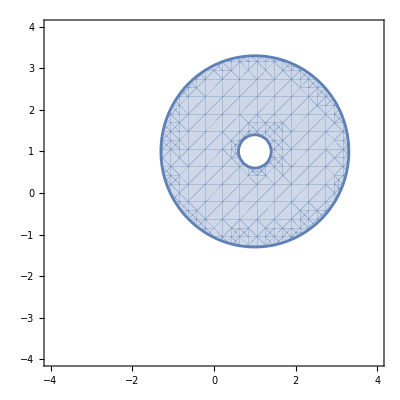

```mathematica
{z0,R1,R2}={1+ⅈ,0.4,2.3};
ComplexRegionPlot[ R1<Abs[z-z0]<R2,{z,4},
Axes->True]
```

### Types of Singularities

Removable:   Fake singularity does not show up in TS.

```mathematica
Series[Sin[z]/z,{z,0,5}]
```

1-z^2/6+z^4/120+O[z]^6

Poles:   Terminating “negative” powers in Laurent Series
	f(z)=∑_(k=-N)^∞ (a_k(z-z_0))^k
a_-N is the strength of the pole z_0.  a_-1 is the residue at the pole.

```mathematica
Series[Sin[z]/z,{z,0,5}]
```

Essential Singularity:   You need the LS sum to go to -∞. In words a_k≠0 for an infinite number of negative indices. As aways a_-1 is the residue.

Branch Point:   TS and LS are single valued.  Perhaps surprisingly LS can have branch cuts inside the inner donut radius!

## Example 4.26 p111

Describe possible expansions (Taylor and Laurent) for (z^2-1)^(1/2) about z=0.

```mathematica
f1[z_]:=(z^2-1)^(1/2)
f2[z_]:=ⅈ(1-z^2)^(1/2)
f3[z_]:=(z-1)^(1/2)(z+1)^(1/2)
TabView[{
"f1"->ComplexPlot3D[f1[z],{z,3}],
"f2"->ComplexPlot3D[f2[z],{z,3}],
"f3"->ComplexPlot3D[f3[z],{z,3}]
}]
```

123